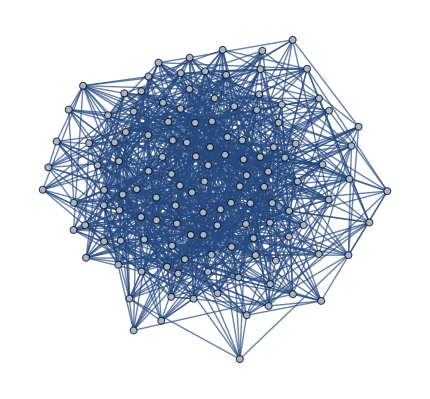

```mathematica
g = RandomGraph[{128 , 1024}]
```

```mathematica
Export[NotebookDirectory[]<>"randgraph",{#[[1]] , #[[2]] , RandomReal[{0.5 , 1.5}]}&/@EdgeList[g] , "Table"]
```

/home/kacper/GIT_HUB/quick_note/NOTES/1515260167183_c71ec7ef-1cb2-44a9-8720-ff42665d5ebc/FILES/kacpertopol.github.io/start/pl/010_Nauczanie/005_Algorytmy_i_Struktury_Danych_(lab_komputerowe,_lato_2019-2020)/001_Zestawy_zadań/012_Zestaw_12_(19_V_2020)/randgraph